```mathematica
SetDirectory[NotebookDirectory[]];
```

# SEP on lattice

## Import Gillespie

```mathematica
<<GillespieLattice1D`
```

## Extra functions for stoch simulations

Moments from h,j vals

```mathematica
fMomentsFromhj[iVals_,nVal_]:=Module[
{terms,nt,m,reps,vals,vecs,u,dm1,dl1,p,l1,l2,l3,l4,l5,matr1}
,
terms={ha,hb,hc,hd,jaa,jab,jac,jad,jbb,jbc,jbd,jcc,jcd,jdd};
nt=Length[terms];

reps={ha->iVals[[1]],hb->iVals[[2]],hc->iVals[[3]],hd->iVals[[4]],jaa->iVals[[5]],jab->iVals[[6]],jac->iVals[[7]],jad->iVals[[8]],jbb->iVals[[9]],jbc->iVals[[10]],jbd->iVals[[11]],jcc->iVals[[12]],jcd->iVals[[13]],jdd->iVals[[14]],n->nVal};

m={
{1,Exp[ha/2],Exp[hb/2],Exp[hc/2],Exp[hd/2]},
{Exp[ha/2],Exp[ha+jaa],Exp[hb/2+ha/2+jab],Exp[hc/2+ha/2+jac],Exp[hd/2+ha/2+jad]},
{Exp[hb/2],Exp[ha/2+hb/2+jab],Exp[hb+jbb],Exp[hc/2+hb/2+jbc],Exp[hd/2+hb/2+jbd]},
{Exp[hc/2],Exp[ha/2+hc/2+jac],Exp[hb/2+hc/2+jbc],Exp[hc+jcc],Exp[hd/2+hc/2+jcd]},
{Exp[hd/2],Exp[ha/2+hd/2+jad],Exp[hb/2+hd/2+jbd],Exp[hc/2+hd/2+jcd],Exp[hd+jdd]}
};

(* First derivatives of matrix *)
dm1=Association[];
Do[
dm1[i]=D[m,terms[[i]]]/.reps;
,{i,1,nt}];

(* Eigenvalues are in order high -> low *)
{{l1,l2,l3,l4,l5},vecs}=Eigensystem[m/.reps];
u=Normalize/@vecs;

(* First derivative of largest eigenvalue *)
dl1=Association[];
p=Association[];
Do[
p[i]=Association[];
Do[
p[i][iu]=u[[1]].dm1[i].u[[iu]];
,{iu,1,5}];
dl1[i]=p[i][1];
,{i,1,nt}];

(* First derivative of n*Log(lambda) *)
matr1=ConstantArray[0,nt];
Do[
matr1[[i]]=nVal*dl1[i]/l1;
,{i,1,nt}];

Return[matr1]
];
```

### Test

```mathematica
iValsTest=RandomReal[{-1,1},14];
```

```mathematica
fMomentsFromhj[iValsTest,100]
```

{4.46306,19.3872,34.5592,35.8162,0.621364,1.75034,2.86303,2.11087,2.68883,11.8367,16.9006,12.3107,26.4374,11.4771}

BM learning to get h,j from lattice

```mathematica
runBMlattice[lattice_,nIterBM_,iVals0_,nChain_,lambdaMaxArr_,storeValsFlag_]:=Module[
{momentsAwake},
momentsAwake={fMean[lattice,"S"],fMean[lattice,"E"],fMean[lattice,"X"],fMean[lattice,"P"],
fNN[lattice,"S","S"],fNN[lattice,"S","E"],fNN[lattice,"S","X"],fNN[lattice,"S","P"],
fNN[lattice,"E","E"],fNN[lattice,"E","X"],fNN[lattice,"E","P"],
fNN[lattice,"X","X"],fNN[lattice,"X","P"],
fNN[lattice,"P","P"]}//N;
Return[runBMlatticeGivenAwake[nIterBM,iVals0,nChain,momentsAwake,lambdaMaxArr,storeValsFlag]];
];
```

```mathematica
runBMlatticeGivenAwake[nIterBM_,iVals0_,nChain_,momentsAwake_,lambdaMaxArr_,storeValsFlag_]:=Module[
{iVals,iValsSt,momentsAsleep,dVals,maxUpdate}
,
(* Initial guess for vals *)
iVals=iVals0;
If[storeValsFlag,iValsSt={iVals};];

(* Pass over the data multiple times *)
Monitor[
Do[
(* Asleep phase *)
momentsAsleep=fMomentsFromhj[iVals,nChain]//N;

(* Update *)
dVals =momentsAwake-momentsAsleep;

(* Fix the magnitudes *)
maxUpdate=Max[Abs[dVals]];
If[maxUpdate>lambdaMaxArr[[iIter]],
dVals*=lambdaMaxArr[[iIter]]/maxUpdate;
];

(* Decrease *)
iVals+=dVals;
If[storeValsFlag,AppendTo[iValsSt,iVals]];

,{iIter,nIterBM}];

,
ProgressIndicator[iIter,{1,nIterBM}]
];

If[storeValsFlag,Return[{iVals,iValsSt}]];
Return[iVals];
]
```

## Stochastic simulations

Parameters

```mathematica
nChain=100;
```

```mathematica
tMax=1.0;
dt=0.01;
```

```mathematica
k1b=0.1;
k2f=0.5;
```

```mathematica
prob1f=0.1;
```

```mathematica
nTrials=100;
```

```mathematica
hS0=0.5;
hE0=1.0;
hX0=-1.0;
hP0=-1.0;

jSS0=0.0;
jSE0=0.0;
jSX0=0.0;
jSP0=0.0;

jEE0=0.0;
jEX0=0.0;
jEP0=0.0;

jXX0=0.0;
jXP0=0.0;

jPP0=0.0;
```

```mathematica
orderMean={"S","E","X","P"};
orderNN={{"S","S"},{"S","E"},{"S","X"},{"S","P"},
{"E","E"},{"E","X"},{"E","P"},
{"X","X"},{"X","P"},
{"P","P"}};
```

Reactions

```mathematica
uniRxnList={
fReactionUnimol["1b",k1b,{"X"},{"S","E"}],
fReactionUnimol["2f",k2f,{"X"},{"P","E"}]
};
```

```mathematica
biRxnList={
fReactionBimol["1f",prob1f,{"S","E"},{"X"}]
};
```

IC

```mathematica
(* Moments *)
iVals0={hS0,hE0,hX0,hP0,
jSS0,jSE0,jSX0,jSP0,
jEE0,jEX0,jEP0,
jXX0,jXP0,
jPP0};
fMomentsFromhj[iVals0,nChain]
```

{27.016,44.5418,6.02808,6.02808,7.29863,24.0668,3.25709,3.25709,19.8397,5.37004,5.37004,0.363378,0.726755,0.363378}

### Method 1: By hand

```mathematica
Map[IntegerPart[#]&,fMomentsFromhj[iVals0,nChain]]
```

{27,44,6,6,7,24,3,3,19,5,5,0,0,0}

```mathematica
(* Make a lattice by hand *)
lattice0=ConstantArray[0,nChain];
Do[
lattice0[[i]]=fMol["S",i];
,{i,1,8,1}];
Do[
lattice0[[i]]=fMol["X",i];
,{i,15,18,1}];
Do[
lattice0[[i]]=fMol["P",i];
,{i,25,28,1}];
Do[
lattice0[[i]]=fMol["E",i];
,{i,76,100,1}];

Do[
lattice0[[i]]=fMol["S",i];
lattice0[[i+1]]=fMol["E",i+1];
,{i,35,53,2}];

Do[
lattice0[[i]]=fMol["S",i];
,{i,{14,19,24,29}}];

Do[
lattice0[[i]]=fMol["S",i];
lattice0[[i+1]]=fMol["X",i+1];
,{i,56,58,2}];
Do[
lattice0[[i]]=fMol["S",i];
lattice0[[i+1]]=fMol["P",i+1];
,{i,61,63,2}];

Do[
lattice0[[i]]=fMol["E",i];
,{i,{10,12,21,31,33,66,68,70,72}}];
lattice0[[74]]=fMol["S",74];
```

```mathematica
(* Check moments *)
```

```mathematica
{fMean[lattice0,"S"],fMean[lattice0,"E"],fMean[lattice0,"X"],fMean[lattice0,"P"],
fNN[lattice0,"S","S"],fNN[lattice0,"S","E"],fNN[lattice0,"S","X"],fNN[lattice0,"S","P"],
fNN[lattice0,"E","E"],fNN[lattice0,"E","X"],fNN[lattice0,"E","P"],
fNN[lattice0,"X","X"],fNN[lattice0,"X","P"],
fNN[lattice0,"P","P"]}
```

{27,44,6,6,7,19,5,5,24,0,0,3,0,3}

```mathematica
Map[IntegerPart[#]&,fMomentsFromhj[iVals0,nChain]]
```

{27,44,6,6,7,24,3,3,19,5,5,0,0,0}

### Method 2: Gibbs sampling

```mathematica
(* Generate initial lattice *)
hDict=<|"S"->hS0,"E"->hE0,"X"->hX0,"P"->hP0|>;
jDict=<|
{"S","S"}->jSS0,{"E","E"}->jEE0,{"X","X"}->jXX0,{"P","P"}->jPP0,
{"S","E"}->jSE0,{"S","X"}->jSX0,{"S","P"}->jSP0,
{"E","X"}->jEX0,{"E","P"}->jEP0,
{"X","P"}->jXP0
|>;
lattice0=fGenLattice[hDict,jDict,nChain,1000];
```

```mathematica
(* Use BMLA to get the true initial h,j *)
```

```mathematica
nIterBM=10000;
lambdaInit=0.001;
lambdaFinal=0.000001;
lambdak=2.0;
lambdaMaxArr=Table[(ⅇ^lambdak (lambdaInit-lambdaFinal))/(-1+ⅇ^lambdak)*Exp[-lambdak*(i-1)/(nIterBM-1)]+(-lambdaInit+ⅇ^lambdak lambdaFinal)/(-1+ⅇ^lambdak),{i,1,nIterBM}];
```

```mathematica
(* The actual h,j *)
{iVals0Final,iVals0TrueSt}=runBMlattice[lattice0,nIterBM,iVals0,nChain,lambdaMaxArr,True];
```

$Aborted

```mathematica
mActual=Table[fMomentsFromhj[iVals0TrueSt[[t]],nChain],{t,1,Length[iVals0TrueSt]}];
```

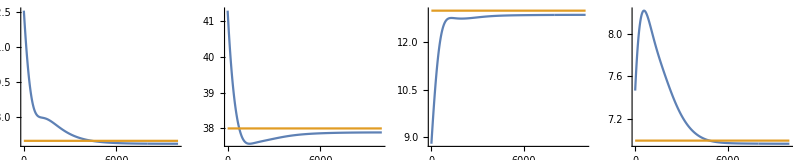

```mathematica
GraphicsRow[
Table[
mTrue=fMean[lattice0,orderMean[[i]]];
mActuali=mActual[[;;,i]];
ListLinePlot[{mActuali,{{0,mTrue},{Length[mActual],mTrue}}},PlotRange->All]
,{i,1,Length[orderMean],1}]
,ImageSize->800]
```

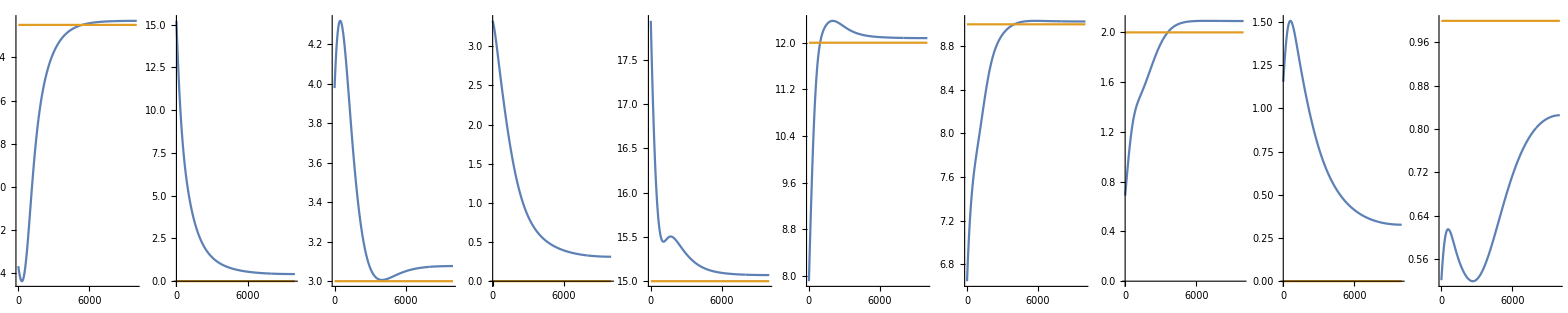

```mathematica
GraphicsRow[
Table[
mTrue=fNN[lattice0,orderNN[[i,1]],orderNN[[i,2]]];
mActuali=mActual[[;;,i+4]];
ListLinePlot[{mActuali,{{0,mTrue},{Length[mActual],mTrue}}},PlotRange->All]
,{i,1,Length[orderNN],1}]
,ImageSize->1800]
```

```mathematica
(* Overwrite *)
{hS0,hE0,hX0,hP0,jSS0,jEE0,jXX0,jPP0,jSE0,jSX0,jSP0,jEX0,jEP0,jXP0}=iVals0TrueSt[[-1]];
iVals0=iVals0TrueSt[[-1]];
iVals0
```

{-0.125555,1.32391,-0.355387,-1.41853,1.31117,-3.79161,-0.412326,-1.86208,-0.639075,-0.173742,0.372928,0.145301,-1.56575,0.891996}

```mathematica
(* Final moments *)
fMomentsFromhj[iVals0TrueSt[[-1]],nChain]
```

{16.8764,37.8881,12.8674,6.97089,11.075,0.41651,3.07658,0.312238,15.0689,12.0793,9.02605,2.09127,0.326875,0.825609}

Run

```mathematica
(* Do some number of trials*)
meanSt=Association[];
Do[
meanSt[o]={};
,{o,orderMean}];
nnSt=Association[];
Do[
nnSt[o]={};
,{o,orderNN}];
Monitor[
Do[
(* Do it *)
lattice=fGillespie[tMax,dt,lattice0,uniRxnList,biRxnList];

(* Calculate mean, NN *)
Do[
AppendTo[meanSt[o],Table[fMean[lattice[t],o],{t,Keys[lattice]}]];
,{o,orderMean}];
Do[
AppendTo[nnSt[o],Table[fNN[lattice[t],o[[1]],o[[2]]],{t,Keys[lattice]}]];
,{o,orderNN}];

,{iTrial,nTrials}];
,
ProgressIndicator[iTrial,{1,nTrials}]
];
```

Convert to h,j

```mathematica
nIterBM=100;
lambdaInit=0.001;
lambdaFinal=0.000001;
lambdak=2.0;
lambdaMaxArr=Table[(ⅇ^lambdak (lambdaInit-lambdaFinal))/(-1+ⅇ^lambdak)*Exp[-lambdak*(i-1)/(nIterBM-1)]+(-lambdaInit+ⅇ^lambdak lambdaFinal)/(-1+ⅇ^lambdak),{i,1,nIterBM}];
```

```mathematica
momsAwake={
Mean[meanSt["S"]],Mean[meanSt["E"]],Mean[meanSt["X"]],Mean[meanSt["P"]],
Mean[nnSt[{"S","S"}]],Mean[nnSt[{"S","E"}]],Mean[nnSt[{"S","X"}]],Mean[nnSt[{"S","P"}]],
Mean[nnSt[{"E","E"}]],Mean[nnSt[{"E","X"}]],Mean[nnSt[{"E","P"}]],
Mean[nnSt[{"X","X"}]],Mean[nnSt[{"X","P"}]],
Mean[nnSt[{"P","P"}]]
}//N;
```

```mathematica
momsAwakeLP={};
Do[
AppendTo[momsAwakeLP,LowpassFilter[m,0.5]];
,{m,momsAwake}];
```

```mathematica
iValsSt={iVals0};
Monitor[
Do[
AppendTo[iValsSt,runBMlatticeGivenAwake[nIterBM,iValsSt[[-1]],nChain,momsAwake[[;;,im]],lambdaMaxArr,False]];
,{im,1,Length[momsAwake[[1]]]}]
,
ProgressIndicator[im,{1,Length[momsAwake[[1]]]}]
]
```

### Trajectories in h,j space

#### controlling means

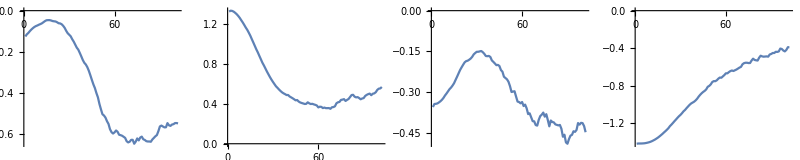

```mathematica
GraphicsRow[
Table[
ListLinePlot[iValsSt[[;;,i]]]
,{i,1,4}],
ImageSize->800]
```

#### means

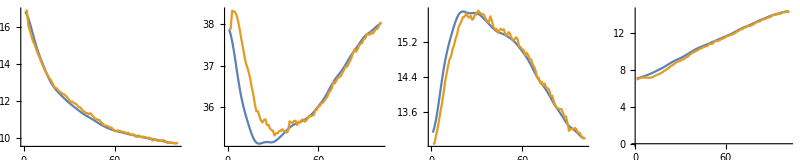

```mathematica
GraphicsRow[
Table[
ListLinePlot[{momsAwakeLP[[j]]//N,Table[fMomentsFromhj[iValsSt[[i]],nChain][[j]],{i,1,Length[iValsSt]}]},PlotRange->All]
,{j,1,4}],
ImageSize->800]
```

#### controlling NN

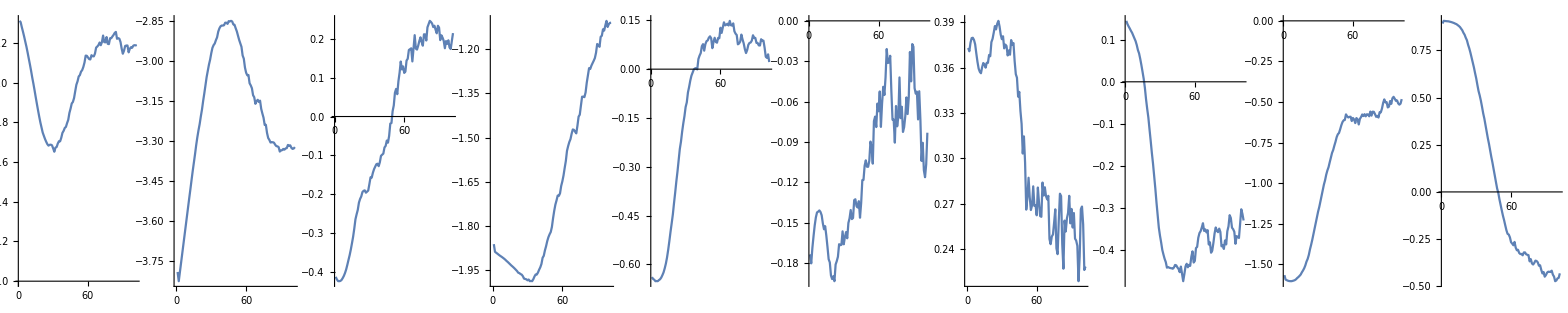

```mathematica
GraphicsRow[
Table[
ListLinePlot[iValsSt[[;;,i]]]
,{i,5,14}],
ImageSize->1800]
```

#### NN

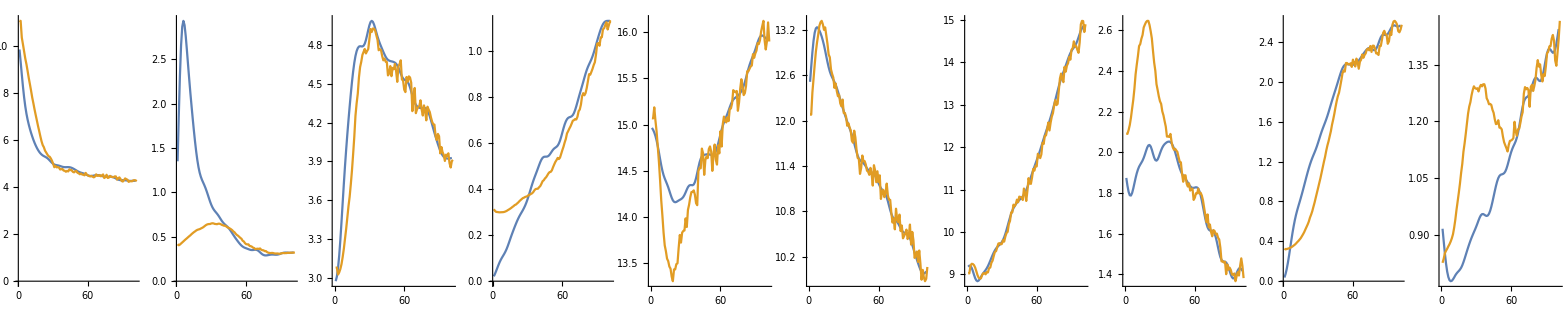

```mathematica
GraphicsRow[
Table[
ListLinePlot[{momsAwakeLP[[j]],Table[fMomentsFromhj[iValsSt[[i]],nChain][[j]],{i,1,Length[iValsSt]}]},PlotRange->All]
,{j,5,14}],
ImageSize->1800]
```

## Basis functions of A+B -> C

Partition func matrix

```mathematica
fmatrFWD[haVal_,hbVal_,hcVal_,jaaVal_,jabVal_,jacVal_,jbbVal_,jbcVal_,jccVal_,nVal_]:=Module[
{terms,nt,m,reps,vals,vecs,u,dm1,dm2,dl1,p,dl2,l1,l2,l3,l4,matr1,matr2}
,
terms={ha,hb,hc,jaa,jab,jac,jbb,jbc,jcc};
nt=Length[terms];

reps={ha->haVal,hb->hbVal,hc->hcVal,jaa->jaaVal,jab->jabVal,jac->jacVal,jbb->jbbVal,jbc->jbcVal,jcc->jccVal,n->nVal};

m={
{1,Exp[ha/2],Exp[hb/2],Exp[hc/2]},
{Exp[ha/2],Exp[ha+jaa],Exp[hb/2+ha/2+jab],Exp[hc/2+ha/2+jac]},
{Exp[hb/2],Exp[ha/2+hb/2+jab],Exp[hb+jbb],Exp[hc/2+hb/2+jbc]},
{Exp[hc/2],Exp[ha/2+hc/2+jac],Exp[hb/2+hc/2+jbc],Exp[hc+jcc]}
};

(* First derivatives of matrix *)
dm1=Association[];
Do[
dm1[i]=D[m,terms[[i]]]/.reps;
,{i,1,nt}];

(* Second derivatives *)
dm2=Association[];
Do[
Do[
dm2[{i,j}]=D[m,terms[[i]],terms[[j]]]/.reps;
,{j,i,nt}];
,{i,1,nt}];

(* Eigenvalues are in order high -> low *)
{{l1,l2,l3,l4},vecs}=Eigensystem[m/.reps];
u=Normalize/@vecs;

(* First derivative of largest eigenvalue *)
dl1=Association[];
p=Association[];
Do[
p[i]=Association[];
Do[
p[i][iu]=u[[1]].dm1[i].u[[iu]];
,{iu,1,4}];
dl1[i]=p[i][1];
,{i,1,nt}];

(* Second derivatives *)
dl2=Association[];
Do[
Do[
dl2[{i,j}]=u[[1]].dm2[{i,j}].u[[1]]+2*(
p[i][2]*p[j][2]/(l1-l2)
+p[i][3]*p[j][3]/(l1-l3)
+p[i][4]*p[j][4]/(l1-l4)
);
,{j,i,nt}];
,{i,1,nt}];

(* First derivative of n*Log(lambda) *)
matr1=ConstantArray[0,nt];
Do[
matr1[[i]]=nVal*dl1[i]/l1;
,{i,1,nt}];

(* Second derivative of n*Log(lambda) *)
matr2=ConstantArray[0,{nt,nt}];
Do[
Do[
matr2[[i,j]]=nVal*(dl2[{i,j}]-dl1[i]*dl1[j]/l1)/l1;
,{j,i,nt}];

(* Symmetric matrix *)
Do[
matr2[[i,j]]=matr2[[j,i]];
,{j,1,i-1}];
,{i,1,nt}];

Return[{matr1,matr2}]
];
```

### Test

```mathematica
reps={ha->RandomReal[{-1,1}],hb->RandomReal[{-1,1}],hc->RandomReal[{-1,1}],jaa->RandomReal[{-1,1}],jab->RandomReal[{-1,1}],jac->RandomReal[{-1,1}],jbb->RandomReal[{-1,1}],jbc->RandomReal[{-1,1}],jcc->RandomReal[{-1,1}],n->100.0};
```

```mathematica
fmatrFWD[ha/.reps,hb/.reps,hc/.reps,jaa/.reps,jab/.reps,jac/.reps,jbb/.reps,jbc/.reps,jcc/.reps,n/.reps][[2]]
```

{{30.2104,-14.6697,-4.60189,38.0675,-8.66389,-1.70847,-4.87347,-2.33208,-1.07116},{-14.6697,14.9801,-0.279142,-20.0671,14.5933,-0.804737,5.3541,0.865934,-0.134684},{-4.60189,-0.279142,4.00666,-4.94995,-1.69887,2.60198,-0.151153,1.41294,1.11522},{38.0675,-20.0671,-4.94995,53.0182,-18.3074,-2.47146,-5.24431,-2.36042,-1.03737},{-8.66389,14.5933,-1.69887,-18.3074,25.9303,-1.3776,1.83574,-0.143542,-0.386736},{-1.70847,-0.804737,2.60198,-2.47146,-1.3776,3.3237,-0.22252,0.477524,0.402655},{-4.87347,5.3541,-0.151153,-5.24431,1.83574,-0.22252,4.12654,0.113084,-0.0402056},{-2.33208,0.865934,1.41294,-2.36042,-0.143542,0.477524,0.113084,1.57807,0.218802},{-1.07116,-0.134684,1.11522,-1.03737,-0.386736,0.402655,-0.0402056,0.218802,0.667425}}

### Check

```mathematica
m={
{1,Exp[ha/2],Exp[hb/2],Exp[hc/2]},
{Exp[ha/2],Exp[ha+jaa],Exp[hb/2+ha/2+jab],Exp[hc/2+ha/2+jac]},
{Exp[hb/2],Exp[ha/2+hb/2+jab],Exp[hb+jbb],Exp[hc/2+hb/2+jbc]},
{Exp[hc/2],Exp[ha/2+hc/2+jac],Exp[hb/2+hc/2+jbc],Exp[hc+jcc]}
};
```

```mathematica
(* largest eigenvalue*)
```

```mathematica
lp=Eigenvalues[m,Quartics->True][[-1]];
```

```mathematica
(* First component of the matrix *)
```

```mathematica
D[n*Log[lp],{ha,2}]/.reps
```

30.2104+5.74423×10^-16 ⅈ

Triplet moment

```mathematica
ftripletFWD[x_,y_,z_,haVal_,hbVal_,hcVal_,jaaVal_,jabVal_,jacVal_,jbbVal_,jbcVal_,jccVal_,nVal_]:=Module[
{rdx,rdz,rhx,rhy,rhz,rjxy,rjyz,hjreps,
vals,vecs,u,reps,ureps,lreps,aveSimpz,m},
If[x=="A",rdx={dxa->1,dxb->0,dxc->0};rhx={hx->haVal};];
If[x=="B",rdx={dxa->0,dxb->1,dxc->0};rhx={hx->hbVal};];
If[x=="C",rdx={dxa->0,dxb->0,dxc->1};rhx={hx->hcVal};];
If[z=="A",rdz={dza->1,dzb->0,dzc->0};rhz={hz->haVal};];
If[z=="B",rdz={dza->0,dzb->1,dzc->0};rhz={hz->hbVal};];
If[z=="C",rdz={dza->0,dzb->0,dzc->1};rhz={hz->hcVal};];
If[y=="A",rhy={hy->haVal};];
If[y=="B",rhy={hy->hbVal};];
If[y=="C",rhy={hy->hcVal};];
If[x=="A"&&y=="A",rjxy={jxy->jaaVal}];
If[(x=="A"&&y=="B")||(x=="B"&&y=="A"),rjxy={jxy->jabVal}];
If[(x=="A"&&y=="C")||(x=="C"&&y=="A"),rjxy={jxy->jacVal}];
If[x=="B"&&y=="B",rjxy={jxy->jbbVal}];
If[(x=="B"&&y=="C")||(x=="C"&&y=="B"),rjxy={jxy->jbcVal}];
If[x=="C"&&y=="C",rjxy={jxy->jccVal}];
If[y=="A"&&z=="A",rjyz={jyz->jaaVal}];
If[(y=="A"&&z=="B")||(y=="B"&&z=="A"),rjyz={jyz->jabVal}];
If[(y=="A"&&z=="C")||(y=="C"&&z=="A"),rjyz={jyz->jacVal}];
If[y=="B"&&z=="B",rjyz={jyz->jbbVal}];
If[(y=="B"&&z=="C")||(y=="C"&&z=="B"),rjyz={jyz->jbcVal}];
If[y=="C"&&z=="C",rjyz={jyz->jccVal}];

hjreps={ha->haVal,hb->hbVal,hc->hcVal,jaa->jaaVal,jab->jabVal,jac->jacVal,jbb->jbbVal,jbc->jbcVal,jcc->jccVal};

reps=Join[rdx,rdz,rhx,rhy,rhz,rjxy,rjyz,{n->nVal},hjreps];

m={
{1,Exp[ha/2],Exp[hb/2],Exp[hc/2]},
{Exp[ha/2],Exp[ha+jaa],Exp[hb/2+ha/2+jab],Exp[hc/2+ha/2+jac]},
{Exp[hb/2],Exp[ha/2+hb/2+jab],Exp[hb+jbb],Exp[hc/2+hb/2+jbc]},
{Exp[hc/2],Exp[ha/2+hc/2+jac],Exp[hb/2+hc/2+jbc],Exp[hc+jcc]}
}/.reps;

{vals,vecs}=Eigensystem[m];
u=Normalize/@vecs;

ureps=Flatten[Table[ToExpression["u"<>ToString[i]<>ToString[j]]->u[[i,j]],{i,1,4},{j,1,4}],1];
lreps=Table[ToExpression["l"<>ToString[i]]->vals[[i]],{i,1,4}];

reps=Join[reps,ureps,lreps];

aveSimpz=(ⅇ^(hx/2+hy+hz/2+jxy+jyz) l1^(-3+n) n (dxa u12+dxb u13+dxc u14) (dza u12+dzb u13+dzc u14) (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)^2)/(l1^(-1+n) u11 (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)+l2^(-1+n) u21 (u21+ⅇ^(ha/2) u22+ⅇ^(hb/2) u23+ⅇ^(hc/2) u24)+l3^(-1+n) u31 (u31+ⅇ^(ha/2) u32+ⅇ^(hb/2) u33+ⅇ^(hc/2) u34)+l4^(-1+n) u41 (u41+ⅇ^(ha/2) u42+ⅇ^(hb/2) u43+ⅇ^(hc/2) u44)+ⅇ^(ha/2) (l1^(-1+n) u12 (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)+l2^(-1+n) u22 (u21+ⅇ^(ha/2) u22+ⅇ^(hb/2) u23+ⅇ^(hc/2) u24)+l3^(-1+n) u32 (u31+ⅇ^(ha/2) u32+ⅇ^(hb/2) u33+ⅇ^(hc/2) u34)+l4^(-1+n) u42 (u41+ⅇ^(ha/2) u42+ⅇ^(hb/2) u43+ⅇ^(hc/2) u44))+ⅇ^(hb/2) (l1^(-1+n) u13 (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)+l2^(-1+n) u23 (u21+ⅇ^(ha/2) u22+ⅇ^(hb/2) u23+ⅇ^(hc/2) u24)+l3^(-1+n) u33 (u31+ⅇ^(ha/2) u32+ⅇ^(hb/2) u33+ⅇ^(hc/2) u34)+l4^(-1+n) u43 (u41+ⅇ^(ha/2) u42+ⅇ^(hb/2) u43+ⅇ^(hc/2) u44))+ⅇ^(hc/2) (l1^(-1+n) u14 (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)+l2^(-1+n) u24 (u21+ⅇ^(ha/2) u22+ⅇ^(hb/2) u23+ⅇ^(hc/2) u24)+l3^(-1+n) u34 (u31+ⅇ^(ha/2) u32+ⅇ^(hb/2) u33+ⅇ^(hc/2) u34)+l4^(-1+n) u44 (u41+ⅇ^(ha/2) u42+ⅇ^(hb/2) u43+ⅇ^(hc/2) u44)));

Return[aveSimpz/.reps]
];
```

Time derivatives of the moments

```mathematica
fdmomentsFWD[kf_,matr1_,trip_]:=Module[
{der}
,
(* 
Order of matrix in derivatives of log(Z)=n*log(lambda)
ha,hb,hc,jaa,jab,jac,jbb,jbc,jcc
Recall that jab controls the sum of both moments: < a(i) b(i+1) > + < b(i) a(i+1) > 
*)

(* Order of derivatives: same *)

(* Order of triplet moments:
aab, aba, baa, abb, bab, bba, abc, bac, cab, cba
*)

der=ConstantArray[0,9];
der[[1]]=-kf*matr1[[5]];
der[[2]]=-kf*matr1[[5]];
der[[3]]=kf*matr1[[5]];
der[[4]]=-kf*trip[[1]];
der[[5]]=-kf*matr1[[5]]-kf*trip[[2]]-kf*trip[[5]];
der[[6]]=0.5*kf*trip[[1]]+kf*trip[[2]]-kf*trip[[9]]+0.5*kf*trip[[3]];
der[[7]]=-kf*trip[[6]];
der[[8]]=kf*trip[[5]]+0.5*kf*trip[[6]]+0.5*kf*trip[[4]]-kf*trip[[10]];
der[[9]]=0.5*kf*trip[[7]]+0.5*kf*trip[[9]]+0.5*kf*trip[[8]]+0.5*kf*trip[[10]];

Return[der];
];
```

Get basis functions

```mathematica
bfsFWD[haVal_,hbVal_,hcVal_,jaaVal_,jabVal_,jacVal_,jbbVal_,jbcVal_,jccVal_,nVal_,kf_]:=Module[
{matr1,matr2,ts,trip,dmoments,bs}
,

(* Get the matrices *)
{matr1,matr2}=fmatrFWD[haVal,hbVal,hcVal,jaaVal,jabVal,jacVal,jbbVal,jbcVal,jccVal,nVal];

(* Get the triplet moments *)
ts={{"A","A","B"},{"A","B","A"},{"B","A","A"},{"A","B","B"},{"B","A","B"},{"B","B","A"},{"A","B","C"},{"B","A","C"},{"C","A","B"},{"C","B","A"}};
trip=ConstantArray[0,10];
Do[
trip[[i]]=ftripletFWD[ts[[i,1]],ts[[i,2]],ts[[i,3]],haVal,hbVal,hcVal,jaaVal,jabVal,jacVal,jbbVal,jbcVal,jccVal,nVal];
,{i,1,10}];

(* Get the time derivatives of the moments *)
dmoments=fdmomentsFWD[kf,matr1,trip];

(* Solve for the basis functions *)
bs=Inverse[matr2].dmoments;

Return[bs]
];
```

### Test

```mathematica
reps={ha->RandomReal[{-1,1}],hb->RandomReal[{-1,1}],hc->RandomReal[{-1,1}],jaa->RandomReal[{-1,1}],jab->RandomReal[{-1,1}],jac->RandomReal[{-1,1}],jbb->RandomReal[{-1,1}],jbc->RandomReal[{-1,1}],jcc->RandomReal[{-1,1}],n->100.0};
```

```mathematica
kf=1.0;
```

```mathematica
bfsFWD[ha/.reps,hb/.reps,hc/.reps,jaa/.reps,jab/.reps,jac/.reps,jbb/.reps,jbc/.reps,jcc/.reps,n/.reps,kf]
```

{-3.03542,-3.01848,-0.949954,2.09522,1.14193,1.17757,2.18863,1.2656,-0.349861}

## Basis functions of C -> A+B

Partition func matrix

```mathematica
fmatrBKWD[haVal_,hbVal_,hcVal_,jaaVal_,jabVal_,jacVal_,jbbVal_,jbcVal_,jccVal_,nVal_]:=Module[
{terms,nt,m,reps,vals,vecs,u,dm1,dm2,dl1,p,dl2,l1,l2,l3,l4,matr1,matr2}
,
terms={ha,hb,hc,jaa,jab,jac,jbb,jbc,jcc};
nt=Length[terms];

reps={ha->haVal,hb->hbVal,hc->hcVal,jaa->jaaVal,jab->jabVal,jac->jacVal,jbb->jbbVal,jbc->jbcVal,jcc->jccVal,n->nVal};

m={
{1,Exp[ha/2],Exp[hb/2],Exp[hc/2]},
{Exp[ha/2],Exp[ha+jaa],Exp[hb/2+ha/2+jab],Exp[hc/2+ha/2+jac]},
{Exp[hb/2],Exp[ha/2+hb/2+jab],Exp[hb+jbb],Exp[hc/2+hb/2+jbc]},
{Exp[hc/2],Exp[ha/2+hc/2+jac],Exp[hb/2+hc/2+jbc],Exp[hc+jcc]}
};

(* First derivatives of matrix *)
dm1=Association[];
Do[
dm1[i]=D[m,terms[[i]]]/.reps;
,{i,1,nt}];

(* Second derivatives *)
dm2=Association[];
Do[
Do[
dm2[{i,j}]=D[m,terms[[i]],terms[[j]]]/.reps;
,{j,i,nt}];
,{i,1,nt}];

(* Eigenvalues are in order high -> low *)
{{l1,l2,l3,l4},vecs}=Eigensystem[m/.reps];
u=Normalize/@vecs;

(* First derivative of largest eigenvalue *)
dl1=Association[];
p=Association[];
Do[
p[i]=Association[];
Do[
p[i][iu]=u[[1]].dm1[i].u[[iu]];
,{iu,1,4}];
dl1[i]=p[i][1];
,{i,1,nt}];

(* Second derivatives *)
dl2=Association[];
Do[
Do[
dl2[{i,j}]=u[[1]].dm2[{i,j}].u[[1]]+2*(
p[i][2]*p[j][2]/(l1-l2)
+p[i][3]*p[j][3]/(l1-l3)
+p[i][4]*p[j][4]/(l1-l4)
);
,{j,i,nt}];
,{i,1,nt}];

(* First derivative of n*Log(lambda) *)
matr1=ConstantArray[0,nt];
Do[
matr1[[i]]=nVal*dl1[i]/l1;
,{i,1,nt}];

(* Second derivative of n*Log(lambda) *)
matr2=ConstantArray[0,{nt,nt}];
Do[
Do[
matr2[[i,j]]=nVal*(dl2[{i,j}]-dl1[i]*dl1[j]/l1)/l1;
,{j,i,nt}];

(* Symmetric matrix *)
Do[
matr2[[i,j]]=matr2[[j,i]];
,{j,1,i-1}];
,{i,1,nt}];

Return[{matr1,matr2}]
];
```

### Test

```mathematica
reps={ha->RandomReal[{-1,1}],hb->RandomReal[{-1,1}],hc->RandomReal[{-1,1}],jaa->RandomReal[{-1,1}],jab->RandomReal[{-1,1}],jac->RandomReal[{-1,1}],jbb->RandomReal[{-1,1}],jbc->RandomReal[{-1,1}],jcc->RandomReal[{-1,1}],n->100.0};
```

```mathematica
fmatrBKWD[ha/.reps,hb/.reps,hc/.reps,jaa/.reps,jab/.reps,jac/.reps,jbb/.reps,jbc/.reps,jcc/.reps,n/.reps][[2]]
```

{{9.25174,-7.83137,1.21354,1.53202,6.70523,5.926,-8.1473,-1.53209,-0.159676},{-7.83137,42.7379,-20.1182,-1.0712,0.565036,-9.65585,42.2074,-1.09184,-6.27727},{1.21354,-20.1182,18.0925,-0.0611123,-2.94341,5.88987,-18.2727,6.05085,7.10682},{1.53202,-1.0712,-0.0611123,0.983517,0.4723,0.426197,-0.935169,-0.212862,-0.0474452},{6.70523,0.565036,-2.94341,0.4723,10.9837,1.02085,-2.40081,-1.64152,-0.983453},{5.926,-9.65585,5.88987,0.426197,1.02085,9.39128,-8.13573,-0.070689,0.988758},{-8.1473,42.2074,-18.2727,-0.935169,-2.40081,-8.13573,47.663,-3.80165,-5.13945},{-1.53209,-1.09184,6.05085,-0.212862,-1.64152,-0.070689,-3.80165,10.6084,0.894558},{-0.159676,-6.27727,7.10682,-0.0474452,-0.983453,0.988758,-5.13945,0.894558,5.33403}}

### Check

```mathematica
m={
{1,Exp[ha/2],Exp[hb/2],Exp[hc/2]},
{Exp[ha/2],Exp[ha+jaa],Exp[hb/2+ha/2+jab],Exp[hc/2+ha/2+jac]},
{Exp[hb/2],Exp[ha/2+hb/2+jab],Exp[hb+jbb],Exp[hc/2+hb/2+jbc]},
{Exp[hc/2],Exp[ha/2+hc/2+jac],Exp[hb/2+hc/2+jbc],Exp[hc+jcc]}
};
```

```mathematica
(* largest eigenvalue*)
```

```mathematica
lp=Eigenvalues[m,Quartics->True][[-1]];
```

```mathematica
(* First component of the matrix *)
```

```mathematica
D[n*Log[lp],{ha,2}]/.reps
```

9.25174+1.66142×10^-16 ⅈ

NNN moment

```mathematica
fnnnBKWD[x_,z_,haVal_,hbVal_,hcVal_,jaaVal_,jabVal_,jacVal_,jbbVal_,jbcVal_,jccVal_,nVal_]:=Module[
{rdx,rdz,rhx,rhz,rjx,rjz,hjreps,
vals,vecs,u,reps,ureps,lreps,aveSimpz,m},
If[x=="A",rdx={dxa->1,dxb->0,dxc->0};rhx={hx->haVal};];
If[x=="B",rdx={dxa->0,dxb->1,dxc->0};rhx={hx->hbVal};];
If[x=="C",rdx={dxa->0,dxb->0,dxc->1};rhx={hx->hcVal};];
If[z=="A",rdz={dza->1,dzb->0,dzc->0};rhz={hz->haVal};];
If[z=="B",rdz={dza->0,dzb->1,dzc->0};rhz={hz->hbVal};];
If[z=="C",rdz={dza->0,dzb->0,dzc->1};rhz={hz->hcVal};];
If[x=="A",rjx={jxa->jaaVal,jxb->jabVal,jxc->jacVal}];
If[x=="B",rjx={jxa->jabVal,jxb->jbbVal,jxc->jbcVal}];
If[x=="C",rjx={jxa->jacVal,jxb->jbcVal,jxc->jccVal}];
If[z=="A",rjz={jaz->jaaVal,jbz->jabVal,jcz->jacVal}];
If[z=="B",rjz={jaz->jabVal,jbz->jbbVal,jcz->jbcVal}];
If[z=="C",rjz={jaz->jacVal,jbz->jbcVal,jcz->jccVal}];

hjreps={ha->haVal,hb->hbVal,hc->hcVal,jaa->jaaVal,jab->jabVal,jac->jacVal,jbb->jbbVal,jbc->jbcVal,jcc->jccVal};

reps=Join[rdx,rdz,rhx,rhz,rjx,rjz,{n->nVal},hjreps];

m={
{1,Exp[ha/2],Exp[hb/2],Exp[hc/2]},
{Exp[ha/2],Exp[ha+jaa],Exp[hb/2+ha/2+jab],Exp[hc/2+ha/2+jac]},
{Exp[hb/2],Exp[ha/2+hb/2+jab],Exp[hb+jbb],Exp[hc/2+hb/2+jbc]},
{Exp[hc/2],Exp[ha/2+hc/2+jac],Exp[hb/2+hc/2+jbc],Exp[hc+jcc]}
}/.reps;

{vals,vecs}=Eigensystem[m];
u=Normalize/@vecs;

ureps=Flatten[Table[ToExpression["u"<>ToString[i]<>ToString[j]]->u[[i,j]],{i,1,4},{j,1,4}],1];
lreps=Table[ToExpression["l"<>ToString[i]]->vals[[i]],{i,1,4}];

reps=Join[reps,ureps,lreps];

aveSimpz=(ⅇ^((hx+hz)/2) (1+ⅇ^(ha+jaz+jxa)+ⅇ^(hb+jbz+jxb)+ⅇ^(hc+jcz+jxc)) l1^(-3+n) n (dxa u12+dxb u13+dxc u14) (dza u12+dzb u13+dzc u14) (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)^2)/(l1^(-1+n) u11 (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)+l2^(-1+n) u21 (u21+ⅇ^(ha/2) u22+ⅇ^(hb/2) u23+ⅇ^(hc/2) u24)+l3^(-1+n) u31 (u31+ⅇ^(ha/2) u32+ⅇ^(hb/2) u33+ⅇ^(hc/2) u34)+l4^(-1+n) u41 (u41+ⅇ^(ha/2) u42+ⅇ^(hb/2) u43+ⅇ^(hc/2) u44)+ⅇ^(ha/2) (l1^(-1+n) u12 (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)+l2^(-1+n) u22 (u21+ⅇ^(ha/2) u22+ⅇ^(hb/2) u23+ⅇ^(hc/2) u24)+l3^(-1+n) u32 (u31+ⅇ^(ha/2) u32+ⅇ^(hb/2) u33+ⅇ^(hc/2) u34)+l4^(-1+n) u42 (u41+ⅇ^(ha/2) u42+ⅇ^(hb/2) u43+ⅇ^(hc/2) u44))+ⅇ^(hb/2) (l1^(-1+n) u13 (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)+l2^(-1+n) u23 (u21+ⅇ^(ha/2) u22+ⅇ^(hb/2) u23+ⅇ^(hc/2) u24)+l3^(-1+n) u33 (u31+ⅇ^(ha/2) u32+ⅇ^(hb/2) u33+ⅇ^(hc/2) u34)+l4^(-1+n) u43 (u41+ⅇ^(ha/2) u42+ⅇ^(hb/2) u43+ⅇ^(hc/2) u44))+ⅇ^(hc/2) (l1^(-1+n) u14 (u11+ⅇ^(ha/2) u12+ⅇ^(hb/2) u13+ⅇ^(hc/2) u14)+l2^(-1+n) u24 (u21+ⅇ^(ha/2) u22+ⅇ^(hb/2) u23+ⅇ^(hc/2) u24)+l3^(-1+n) u34 (u31+ⅇ^(ha/2) u32+ⅇ^(hb/2) u33+ⅇ^(hc/2) u34)+l4^(-1+n) u44 (u41+ⅇ^(ha/2) u42+ⅇ^(hb/2) u43+ⅇ^(hc/2) u44)));

Return[aveSimpz/.reps]
];
```

Time derivatives of the moments

```mathematica
fdmomentsBKWD[kb_,matr1_,nnn_]:=Module[
{der}
,
(* 
Order of matrix in derivatives of log(Z)=n*log(lambda)
ha,hb,hc,jaa,jab,jac,jbb,jbc,jcc
Recall that jab controls the sum of both moments: < a(i) b(i+1) > + < b(i) a(i+1) > 
*)

(* Order of derivatives: same *)

(* Order of nnn moments:
ca,cb,cc
*)

der=ConstantArray[0,9];
der[[1]]=kb*matr1[[5]];
der[[2]]=kb*matr1[[5]];
der[[3]]=-kb*matr1[[5]];
der[[4]]=0.5*kb*nnn[[1]]+0.5*kb*matr1[[6]];
der[[5]]=kb*matr1[[3]]+0.5*kb*nnn[[2]]+0.5*kb*matr1[[8]]+0.5*kb*matr1[[6]]+0.5*kb*nnn[[1]];
der[[6]]=0.5*kb*nnn[[3]]+kb*matr1[[9]]-kb*matr1[[6]];
der[[7]]=0.5*kb*nnn[[2]]+0.5*kb*matr1[[8]];
der[[8]]=0.5*kb*nnn[[3]]+kb*matr1[[9]]-kb*matr1[[8]];
der[[9]]=-2.0*kb*matr1[[9]];

Return[der];
];
```

Get basis functions

```mathematica
bfsBKWD[haVal_,hbVal_,hcVal_,jaaVal_,jabVal_,jacVal_,jbbVal_,jbcVal_,jccVal_,nVal_,kb_]:=Module[
{matr1,matr2,ts,nnn,dmoments,bs}
,

(* Get the matrices *)
{matr1,matr2}=fmatrBKWD[haVal,hbVal,hcVal,jaaVal,jabVal,jacVal,jbbVal,jbcVal,jccVal,nVal];

(* Get the NNN moments *)
ts={{"C","A"},{"C","B"},{"C","C"}};
nnn=ConstantArray[0,3];
Do[
nnn[[i]]=fnnnBKWD[ts[[i,1]],ts[[i,2]],haVal,hbVal,hcVal,jaaVal,jabVal,jacVal,jbbVal,jbcVal,jccVal,nVal];
,{i,1,3}];

(* Get the time derivatives of the moments *)
dmoments=fdmomentsBKWD[kb,matr1,nnn];

(* Solve for the basis functions *)
bs=Inverse[matr2].dmoments;

Return[bs]
];
```

### Test

```mathematica
reps={ha->RandomReal[{-1,1}],hb->RandomReal[{-1,1}],hc->RandomReal[{-1,1}],jaa->RandomReal[{-1,1}],jab->RandomReal[{-1,1}],jac->RandomReal[{-1,1}],jbb->RandomReal[{-1,1}],jbc->RandomReal[{-1,1}],jcc->RandomReal[{-1,1}],n->100.0};
```

```mathematica
kb=1.0;
```

```mathematica
bfsBKWD[ha/.reps,hb/.reps,hc/.reps,jaa/.reps,jab/.reps,jac/.reps,jbb/.reps,jbc/.reps,jcc/.reps,n/.reps,kb]
```

{-237.766,-181.08,-104.347,183.966,173.964,120.484,126.056,93.4287,44.836}

## Basis functions of diffusion

```mathematica
diffusionBFs[h_,j_]:={(8  ⅇ^h (-1+ⅇ^j))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j)))))),-(4  ⅇ^-j (-1+ⅇ^j) (1+ⅇ^(h+j)))/(1+ⅇ^(h+j) (1+√(ⅇ^(-2 (h+j)) (1+4 ⅇ^h-2 ⅇ^(h+j)+ⅇ^(2 (h+j))))))}//N;
```

## ML via ANN

Training data

### Take the training batch as the first half

```mathematica
iMaxTraining=IntegerPart[2*Length[iValsSt]/3];
iValsTraining=iValsSt[[;;iMaxTraining]];
```

### Smooth the data a bit

```mathematica
iValsStLP={};
Do[
AppendTo[iValsStLP,LowpassFilter[iValsSt[[;;,i]],0.5]]
,{i,1,14}];
iValsStLP=Transpose[iValsStLP];
iValsTrainingLP=iValsStLP[[;;iMaxTraining]];
```

```mathematica
Manipulate[
ListLinePlot[{iValsTraining[[;;,i]],iValsTrainingLP[[;;,i]]}]
,{i,1,14,1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

### Smooth the derivs a bit

```mathematica
derivs={};
Do[
AppendTo[derivs,(iValsTrainingLP[[ivs+1]]-iValsTrainingLP[[ivs]])/dt];
,{ivs,1,Length[iValsTrainingLP]-1}];
```

```mathematica
derivsLP={};
Do[
AppendTo[derivsLP,LowpassFilter[derivs[[;;,i]],0.25]]
,{i,1,14}];
derivsLP=Transpose[derivsLP];
```

```mathematica
Manipulate[
ListLinePlot[{derivs[[;;,i]],derivsLP[[;;,i]]}]
,{i,1,14,1}]
```

### Training data

```mathematica
trainingData={};
Do[
{hsVal,heVal,hxVal,hpVal,jssVal,jseVal,jsxVal,jspVal,jeeVal,jexVal,jepVal,jxxVal,jxpVal,jppVal}=iValsTrainingLP[[ivs]];
(* Basis funcs of S + E -> X with rate 1 *)
b1=bfsFWD[hsVal,heVal,hxVal,jssVal,jseVal,jsxVal,jeeVal,jexVal,jxxVal,nChain,1.0];
(* Basis funcs of X -> S + E with rate 1 *)
b2=bfsBKWD[hsVal,heVal,hxVal,jssVal,jseVal,jsxVal,jeeVal,jexVal,jxxVal,nChain,1.0];
(* Basis funcs of X -> E + P with rate 1 *)
b3=bfsBKWD[heVal,hpVal,hxVal,jeeVal,jepVal,jexVal,jppVal,jxpVal,jxxVal,nChain,1.0];
(* Basis funcs of diffusion *)
b4=Join[diffusionBFs[hsVal,jssVal],diffusionBFs[heVal,jeeVal],diffusionBFs[hxVal,jxxVal],diffusionBFs[hpVal,jppVal]];

AppendTo[trainingData,Join[b1,b2,b3,b4]->derivsLP[[ivs]]];
,{ivs,1,Length[iValsTrainingLP]-1}];
```

```mathematica
Manipulate[
ListLinePlot[Keys[trainingData][[;;,i]]]
,{i,1,35,1}]
```

ANN

```mathematica
net=NetChain[{LinearLayer[35],Tanh,LinearLayer[40],Tanh,LinearLayer[40],Tanh,LinearLayer[14]},"Input"->35,"Output"->14]
```

NetChain[]

```mathematica
trained=NetTrain[net,trainingData,MaxTrainingRounds->40000]
```

NetChain[]

Results

```mathematica
trained[Keys[trainingData[[1]]]]
```

{0.54177,-0.537333,0.344007,0.107253,-1.59454,1.61787,-0.0238317,-0.51183,-0.0970151,0.334784,0.0143564,-0.43852,-0.443947,0.127283}

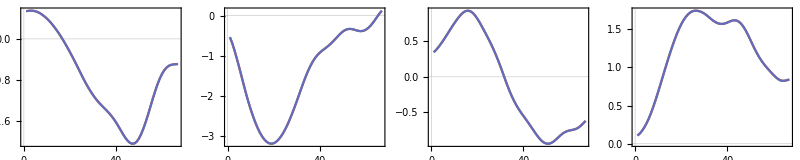

```mathematica
GraphicsRow[
Table[
ListLinePlot[{derivsLP[[;;,j]],Table[trained[Keys[trainingData[[i]]]][[j]],{i,1,Length[trainingData]}]},PlotRange->All]
,{j,1,4}],
ImageSize->800]
```

Plot style

```mathematica
SetOptions[ListLinePlot,{PlotTheme->"Scientific",BaseStyle->{FontSize->30}}];
```

```mathematica
SetOptions[ListContourPlot,{PlotTheme->"Scientific",BaseStyle->{FontSize->30}}];
```

```mathematica
SetOptions[ListLogPlot,{PlotTheme->"Scientific",BaseStyle->{FontSize->30}}];
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x);
```

```mathematica
colorFunc=("DefaultColorFunction"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListContourPlot]));
```

Extrapolate

```mathematica
iValsExt={iValsTraining[[-1]]};
Do[
{hsVal,heVal,hxVal,hpVal,jssVal,jseVal,jsxVal,jspVal,jeeVal,jexVal,jepVal,jxxVal,jxpVal,jppVal}=iValsExt[[-1]];
(* Basis funcs of S + E -> X with rate 1 *)
b1=bfsFWD[hsVal,heVal,hxVal,jssVal,jseVal,jsxVal,jeeVal,jexVal,jxxVal,nChain,1.0];
(* Basis funcs of X -> S + E with rate 1 *)
b2=bfsBKWD[hsVal,heVal,hxVal,jssVal,jseVal,jsxVal,jeeVal,jexVal,jxxVal,nChain,1.0];
(* Basis funcs of X -> E + P with rate 1 *)
b3=bfsBKWD[heVal,hpVal,hxVal,jeeVal,jepVal,jexVal,jppVal,jxpVal,jxxVal,nChain,1.0];
(* Basis funcs of diffusion *)
b4=Join[diffusionBFs[hsVal,jssVal],diffusionBFs[heVal,jeeVal],diffusionBFs[hxVal,jxxVal],diffusionBFs[hpVal,jppVal]];

AppendTo[iValsExt,iValsExt[[-1]]+dt*trained[Join[b1,b2,b3,b4]]];
,{i,1,Length[iValsSt[[iMaxTraining;;]]]}]
```

```mathematica
momentsExt={};
Do[
AppendTo[momentsExt,fMomentsFromhj[ivs,nChain]];
,{ivs,iValsExt}];
```

Plot

```mathematica
pltVline=ListLinePlot[{{iMaxTraining*dt,-100},{iMaxTraining*dt,100}},PlotStyle->Gray];
```

```mathematica
pltiValsExt=
Table[
ListLinePlot[{
Transpose[{Table[j*dt,{j,0,Length[iValsStLP[[;;iMaxTraining,i]]]-1}],iValsStLP[[;;iMaxTraining,i]]}],
Transpose[{Table[(iMaxTraining+j)*dt,{j,-1,Length[iValsStLP[[iMaxTraining;;,i]]]-2}],iValsStLP[[iMaxTraining;;,i]]}],
Transpose[{Table[(iMaxTraining+j)*dt,{j,-1,Length[iValsExt[[;;,i]]]-2}],iValsExt[[;;,i]]}]
},PlotStyle->{colors[[2]],{Dashed,colors[[2]]},colors[[1]]}]
,{i,1,14}];
```

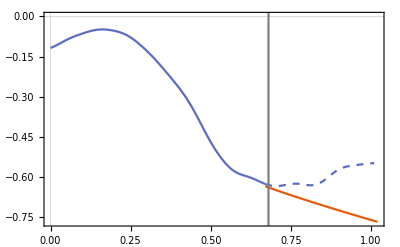

```mathematica
plthS=Show[pltiValsExt[[1]],pltVline]
```

```mathematica
Export["../figures_sep/hS.pdf",plthS];
```

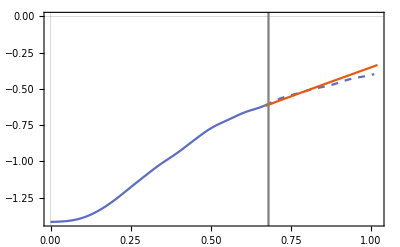

```mathematica
plthP=Show[pltiValsExt[[4]],pltVline]
```

```mathematica
Export["../figures_sep/hP.pdf",plthP];
```

```mathematica
pltMomentsExt=
Table[
ListLinePlot[{
Transpose[{Table[j*dt,{j,0,Length[momsAwakeLP[[i,;;iMaxTraining]]]-1}],momsAwakeLP[[i,;;iMaxTraining]]}],
Transpose[{Table[(iMaxTraining+j)*dt,{j,-1,Length[momsAwakeLP[[i,iMaxTraining;;]]]-2}],momsAwakeLP[[i,iMaxTraining;;]]}],
Transpose[{Table[(iMaxTraining+j)*dt,{j,-1,Length[momentsExt[[;;,i]]]-2}],momentsExt[[;;,i]]}]
},PlotStyle->{colors[[2]],{Dashed,colors[[2]]},colors[[1]]}]
,{i,1,14}];
```

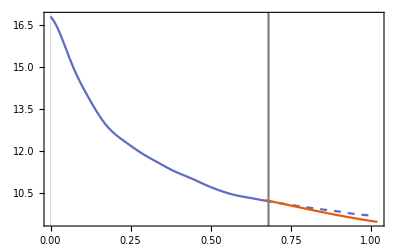

```mathematica
plthSMoment=Show[pltMomentsExt[[1]],pltVline]
```

```mathematica
Export["../figures_sep/hSMoment.pdf",plthSMoment];
```

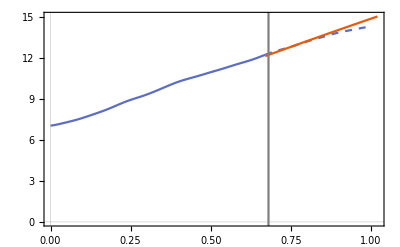

```mathematica
plthPMoment=Show[pltMomentsExt[[4]],pltVline]
```

```mathematica
Export["../figures_sep/hPMoment.pdf",plthPMoment];
```

```mathematica
leg=LineLegend[{colors[[2]],{Dashed,colors[[2]]},colors[[1]]},{"Training data\n(stoch. sim)","Extrapolated\n(stoch. sim)","Extrapolated\n(ANN)"},LabelStyle->{FontSize->20}]
```

```mathematica
Export["../figures_sep/leg.pdf",leg];
```

New uncaptured moment basis function

```mathematica
hSrng={-0.75,0};
hPrng={-1.5,-0.5};
jSPrng={-2.0,-1.4};
hSdom=Range[hSrng[[1]],hSrng[[2]],(hSrng[[2]]-hSrng[[1]])/20.0];
hPdom=Range[hPrng[[1]],hPrng[[2]],(hPrng[[2]]-hPrng[[1]])/20.0];
jSPdom=Range[jSPrng[[1]],jSPrng[[2]],(jSPrng[[2]]-jSPrng[[1]])/20.0];
```

### hS vs hP

```mathematica
tblhsVShp={};
Do[
Do[
{hsVal,heVal,hxVal,hpVal,jssVal,jseVal,jsxVal,jspVal,jeeVal,jexVal,jepVal,jxxVal,jxpVal,jppVal}=iValsTrainingLP[[-1]];
hsVal=hsVal0;
hpVal=hpVal0;
(* Basis funcs of S + E -> X with rate 1 *)
b1=bfsFWD[hsVal,heVal,hxVal,jssVal,jseVal,jsxVal,jeeVal,jexVal,jxxVal,nChain,1.0];
(* Basis funcs of X -> S + E with rate 1 *)
b2=bfsBKWD[hsVal,heVal,hxVal,jssVal,jseVal,jsxVal,jeeVal,jexVal,jxxVal,nChain,1.0];
(* Basis funcs of X -> E + P with rate 1 *)
b3=bfsBKWD[heVal,hpVal,hxVal,jeeVal,jepVal,jexVal,jppVal,jxpVal,jxxVal,nChain,1.0];
(* Basis funcs of diffusion *)
b4=Join[diffusionBFs[hsVal,jssVal],diffusionBFs[heVal,jeeVal],diffusionBFs[hxVal,jxxVal],diffusionBFs[hpVal,jppVal]];

AppendTo[tblhsVShp,{hsVal0,hpVal0,trained[Join[b1,b2,b3,b4]][[8]]}];

,{hpVal0,hPdom}];
,{hsVal0,hSdom}];
```

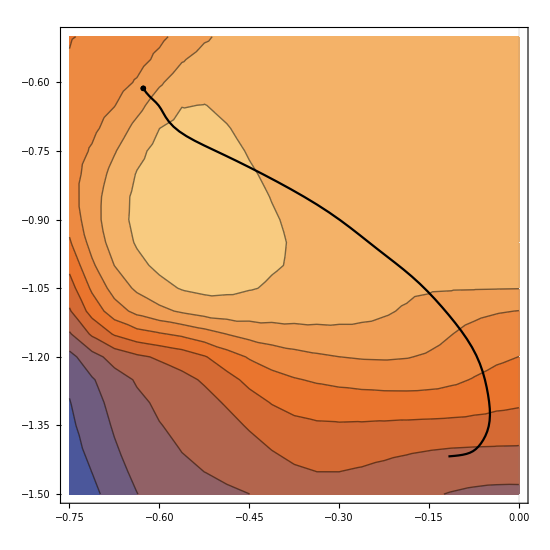

```mathematica
plthsVShp=Show[
ListContourPlot[tblhsVShp],
ListLinePlot[Transpose[{iValsTrainingLP[[;;,1]],iValsTrainingLP[[;;,4]]}],PlotStyle->Black],
ListPlot[{{iValsTrainingLP[[-1,1]],iValsTrainingLP[[-1,4]]}},PlotStyle->Black,PlotMarkers->{Automatic,Large}],
ImageSize->550
]
```

```mathematica
Export["../figures_sep/jSP_hS_hP.pdf",plthsVShp];
```

```mathematica
leghsVShp=BarLegend[{colorFunc,{-0.5,2.0}},LabelStyle->{FontSize->30}]
```

```mathematica
Export["../figures_sep/jSP_hS_hP_leg.pdf",leghsVShp]
```

../figures_sep/jSP_hS_hP_leg.pdf

### hS vs jSP

```mathematica
tbljspVShs={};
Do[
Do[
{hsVal,heVal,hxVal,hpVal,jssVal,jseVal,jsxVal,jspVal,jeeVal,jexVal,jepVal,jxxVal,jxpVal,jppVal}=iValsTrainingLP[[-1]];
hsVal=hsVal0;
jspVal=jspVal0;
(* Basis funcs of S + E -> X with rate 1 *)
b1=bfsFWD[hsVal,heVal,hxVal,jssVal,jseVal,jsxVal,jeeVal,jexVal,jxxVal,nChain,1.0];
(* Basis funcs of X -> S + E with rate 1 *)
b2=bfsBKWD[hsVal,heVal,hxVal,jssVal,jseVal,jsxVal,jeeVal,jexVal,jxxVal,nChain,1.0];
(* Basis funcs of X -> E + P with rate 1 *)
b3=bfsBKWD[heVal,hpVal,hxVal,jeeVal,jepVal,jexVal,jppVal,jxpVal,jxxVal,nChain,1.0];
(* Basis funcs of diffusion *)
b4=Join[diffusionBFs[hsVal,jssVal],diffusionBFs[heVal,jeeVal],diffusionBFs[hxVal,jxxVal],diffusionBFs[hpVal,jppVal]];

AppendTo[tbljspVShs,{hsVal0,jspVal0,trained[Join[b1,b2,b3,b4]][[8]]}];

,{jspVal0,jSPdom}];
,{hsVal0,hSdom}];
```

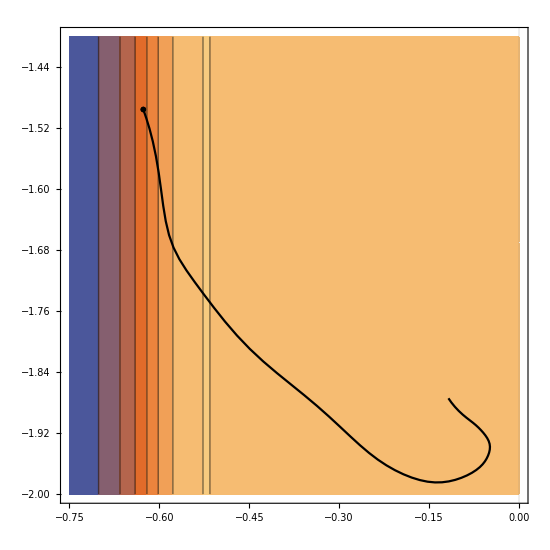

```mathematica
pltjspVShs=Show[
ListContourPlot[tbljspVShs],
ListLinePlot[Transpose[{iValsTrainingLP[[;;,1]],iValsTrainingLP[[;;,8]]}],PlotStyle->Black],
ListPlot[{{iValsTrainingLP[[-1,1]],iValsTrainingLP[[-1,8]]}},PlotStyle->Black,PlotMarkers->{Automatic,Large}],
ImageSize->550
]
```

```mathematica
Export["../figures_sep/jSP_hS_jSP.pdf",pltjspVShs];
```

```mathematica
legjspVShs=BarLegend[{colorFunc,{1.0,1.8}},LabelStyle->{FontSize->30}]
```

```mathematica
Export["../figures_sep/jSP_hS_jSP_leg.pdf",legjspVShs]
```

../figures_sep/jSP_hS_jSP_leg.pdf

### hP vs jSP

```mathematica
tbljspVShp={};
Do[
Do[
{hsVal,heVal,hxVal,hpVal,jssVal,jseVal,jsxVal,jspVal,jeeVal,jexVal,jepVal,jxxVal,jxpVal,jppVal}=iValsTrainingLP[[-1]];
hpVal=hpVal0;
jspVal=jspVal0;
(* Basis funcs of S + E -> X with rate 1 *)
b1=bfsFWD[hsVal,heVal,hxVal,jssVal,jseVal,jsxVal,jeeVal,jexVal,jxxVal,nChain,1.0];
(* Basis funcs of X -> S + E with rate 1 *)
b2=bfsBKWD[hsVal,heVal,hxVal,jssVal,jseVal,jsxVal,jeeVal,jexVal,jxxVal,nChain,1.0];
(* Basis funcs of X -> E + P with rate 1 *)
b3=bfsBKWD[heVal,hpVal,hxVal,jeeVal,jepVal,jexVal,jppVal,jxpVal,jxxVal,nChain,1.0];
(* Basis funcs of diffusion *)
b4=Join[diffusionBFs[hsVal,jssVal],diffusionBFs[heVal,jeeVal],diffusionBFs[hxVal,jxxVal],diffusionBFs[hpVal,jppVal]];

AppendTo[tbljspVShp,{hpVal0,jspVal0,trained[Join[b1,b2,b3,b4]][[8]]}];

,{jspVal0,jSPdom}];
,{hpVal0,hPdom}];
```

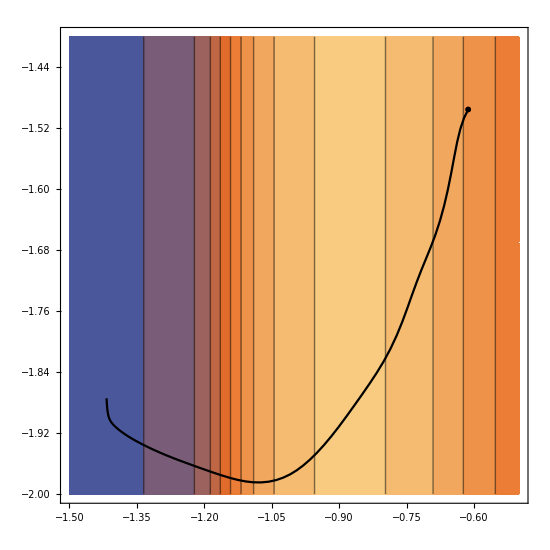

```mathematica
pltjspVShp=Show[
ListContourPlot[tbljspVShp],
ListLinePlot[Transpose[{iValsTrainingLP[[;;,4]],iValsTrainingLP[[;;,8]]}],PlotStyle->Black],
ListPlot[{{iValsTrainingLP[[-1,4]],iValsTrainingLP[[-1,8]]}},PlotStyle->Black,PlotMarkers->{Automatic,Large}],
ImageSize->550
]
```

```mathematica
Export["../figures_sep/jSP_hP_jSP.pdf",pltjspVShp];
```

```mathematica
legjspVShp=BarLegend[{colorFunc,{0.0,2.0}},LabelStyle->{FontSize->30}]
```

```mathematica
Export["../figures_sep/jSP_hP_jSP_leg.pdf",legjspVShp]
```

../figures_sep/jSP_hP_jSP_leg.pdf